```mathematica
dados=Import["/home/afonsolelis/code/afonsolelis/redes_neurais/20230322 - aula 6 e 7/trabalho da aula 5/ibovespa_3.csv","CSV"];
```

```mathematica
valores=ToExpression[dados[[All,1]]];
```

```mathematica
serieTemporal=TimeSeries[valores];
```

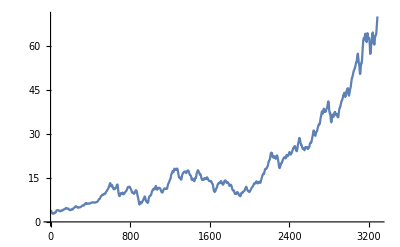

```mathematica
ListLinePlot[%4]
```